### Example: Evolving a 3-mode state through non-linear SFG gate

↓Signal-Idler join Gaussian state in qpqp repressentation after transmission through channel (Used GaussianStates.nb to get expression)

```mathematica
V1={{1/2+Nb (1-η)+Ns η,0,√Ns √(1+Ns) √η Cos[θ],-√Ns √(1+Ns) √η Sin[θ]},{0,1/2+Nb (1-η)+Ns η,-√Ns √(1+Ns) √η Sin[θ],-√Ns √(1+Ns) √η Cos[θ]},{√Ns √(1+Ns) √η Cos[θ],-√Ns √(1+Ns) √η Sin[θ],1/2+Ns,0},{-√Ns √(1+Ns) √η Sin[θ],-√Ns √(1+Ns) √η Cos[θ],0,1/2+Ns}};
V1//MatrixForm
```

(1/2+Nb (1-η)+Ns η | 0 | √Ns √(1+Ns) √η Cos[θ] | -√Ns √(1+Ns) √η Sin[θ]
0 | 1/2+Nb (1-η)+Ns η | -√Ns √(1+Ns) √η Sin[θ] | -√Ns √(1+Ns) √η Cos[θ]
√Ns √(1+Ns) √η Cos[θ] | -√Ns √(1+Ns) √η Sin[θ] | 1/2+Ns | 0
-√Ns √(1+Ns) √η Sin[θ] | -√Ns √(1+Ns) √η Cos[θ] | 0 | 1/2+Ns)

↓Rewriting state in aaa†a† representation.

```mathematica
atoq[2]†.qqpptoqpqp[V1].atoq[2]//FullSimplify//Collect[#,Nb]&//Collect[#,Ns]&//MatrixForm
```

(1/2+Nb (1-η)+Ns η | 0 | 0 | ⅇ^(-ⅈ θ) √Ns √(1+Ns) √η
0 | 1/2+Ns | ⅇ^(-ⅈ θ) √Ns √(1+Ns) √η | 0
0 | ⅇ^(ⅈ θ) √Ns √(1+Ns) √η | 1/2+Nb (1-η)+Ns η | 0
ⅇ^(ⅈ θ) √Ns √(1+Ns) √η | 0 | 0 | 1/2+Ns)

↓Creating the covariance matrix of the state at the input of the first SFG-gate (in qpqp rep. using functions from GaussianStates.nb)

```mathematica
init=1/2 IdentityMatrix[8];(*In qpqp rep, mode orderin: signal, environment, vacuum, idler*)
SIindex=Join[2#-1,2 #]&@{1,4}//Sort;
noiseindex={3,4};(*Ensure that noise mode appears after signal mode in the cov. matrix*)
channel=BSgen[4,1,3,κ].BSgen[4,1,2,η].Phasegen[{θ,0,0,0}].TMSgen[4,1,4,ArcSinh[√Ns]]//qqpptoqpqp[atoq[4].#.atoq[4]†]&;
init[[noiseindex,noiseindex]]+=Nb IdentityMatrix[2];
V2=channel.init.channelᵀ//Part[#,SIindex,SIindex]&//ExpToTrig//Simplify;
V2//MatrixForm
```

(1/2+Ns η κ+Nb (κ-η κ) | 0 | √Ns √(1+Ns) √η √κ Cos[θ] | -√Ns √(1+Ns) √η √κ Sin[θ]
0 | 1/2+Ns η κ+Nb (κ-η κ) | -√Ns √(1+Ns) √η √κ Sin[θ] | -√Ns √(1+Ns) √η √κ Cos[θ]
√Ns √(1+Ns) √η √κ Cos[θ] | -√Ns √(1+Ns) √η √κ Sin[θ] | 1/2+Ns | 0
-√Ns √(1+Ns) √η √κ Sin[θ] | -√Ns √(1+Ns) √η √κ Cos[θ] | 0 | 1/2+Ns)

```mathematica
?Assumptions
```

Assumptions is an option for functions such as Simplify, Refine, and Integrate that specifies default assumptions to be made about symbolic quantities.

```mathematica
#.#ᵀ/2&[atoq[2].#.atoq[2]†&@TMSgen[2,1,2,r]]//MatrixForm
```

(1/2 (Cosh[r]^2+Sinh[r]^2) | Cosh[r] Sinh[r] | 0 | 0
Cosh[r] Sinh[r] | 1/2 (Cosh[r]^2+Sinh[r]^2) | 0 | 0
0 | 0 | 1/2 (Cosh[r]^2+Sinh[r]^2) | -Cosh[r] Sinh[r]
0 | 0 | -Cosh[r] Sinh[r] | 1/2 (Cosh[r]^2+Sinh[r]^2))

↓Symbolically evaluate the density matrix at input of the SFG in the Fock basis (uncomment assignment to variables for numerical evaluation)

```mathematica
Assign[l1_,l2_]:=Table[l1[[i]]-> l2[[i]],{i,Length[l1]}];
```

```mathematica
cov=atoq[2]†.qqpptoqpqp[V2].atoq[2](*/.Assign[{Ns,Nb,θ,η},{0.01,1,0,0.01}]*);
μ=Table[0,4]; (*Mean is zero*)
nmaxvec={3,3};
{time,ρ}=Gaussianrhofockrep[cov,μ,nmaxvec,nmaxvec]//AbsoluteTiming;
ρparam=Compile[{Ns,Nb,θ,η,κ},ρ,CompilationOptions->
{"InlineExternalDefinitions" -> True,
"ExpressionOptimization" -> True}]
```

CompiledFunction[{Ns, Nb, θ, η, κ}, Block[{Compile`$189, Compile`$202, Compile`$203, Compile`$200, Compile`$213, Compile`$224, Compile`$225, Compile`$222, Compile`$238, Compile`$242, Compile`$243, Compile`$259, Compile`$185, Compile`$192, <<2772>>, Compile`$6762, Compile`$2768, Compile`$2771, Compile`$5399, Compile`$5402, Compile`$5415, Compile`$5418}, <<1>>], -CompiledCode-]

↓Plotting the density matrix as a function of θ and Ns

```mathematica
With[{Nb=1,η=0.5,κ=0.2},
Manipulate[MatrixPlot[Chop[#,10^-16],PlotLegends->Automatic,PlotLabel->Tr[#]]&/@{Re[#],Im[#]}&@ρparam[Ns,Nb,θ,η,κ],{Ns,10^-8,1},{θ,0,2π}]]
```

↓SFG Hamiltonian in matrix form

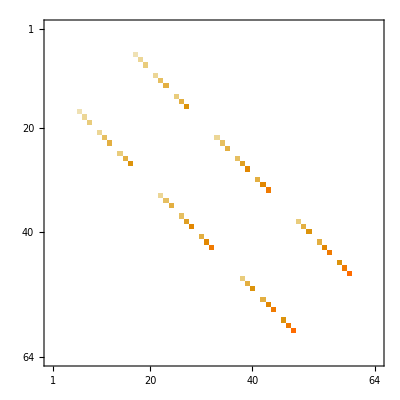

```mathematica
bnmax=3;(*Choosing bnmax to be higher than nmax for signal and idler is pointless, as the higher number states of b will not get excited*)
dimvec=Join[{bnmax+1},Reverse[nmaxvec]+1];(*dimension of the density matrix is one more than max fock number since fock numbers range from 0 to nmax. dimvec={bdim,signaldim,idlerdim*)
{b,as,ai}=Table[If[j==i+1,√i,0],{i,#},{j,#}]&/@dimvec;
Hint=#+#†&@(KroneckerProduct[#1,#2†,#3†]&@@{b,ai,as});
sparseH=SparseArray[Hint];
Hint//MatrixPlot
```

#### Functions for Numerically evolving the state in time

↓The block-ordering of state returned by getρ0 is: b(coarsest), ai(finer), as(finest)

```mathematica
getρ0[Ns_,Nb_,θ_,η_,κ_]:=(*Tensor product of signal-idler joint state with vaccuum b-mode*)KroneckerProduct[Table[Times@@(KroneckerDelta[#,1]&/@{i,j}),{i,bnmax+1},{j,bnmax+1}],ρparam[Ns,Nb,θ,η,κ]//Chop[#,10^-17]&//SparseArray]
```

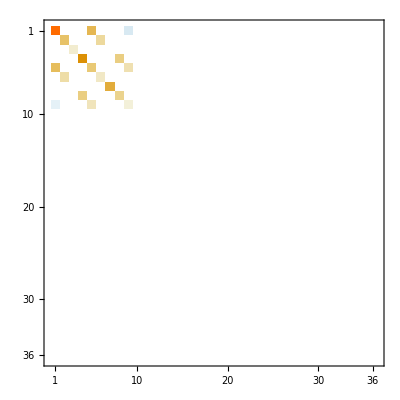

```mathematica
getρ0[0.8,1,0.5,π/3,0.2]//MatrixPlot
```

```mathematica
Clear[getρb];
getρb[Ns_,Nb_,θ_,η_,κ_,gt_]:=(*Compile[{Ns,Nb,η,θ,gtbyhbar},*)Module[{ρb},With[{
ρ0=
getρ0[Ns,Nb,θ,η,κ],
Usfg=MatrixExp[-I gt sparseH]},
(*Print["Trace: ",ρ0//Tr];*)
ρb=PartialTrace[Usfg.ρ0.Usfg†,dimvec,{2,3}]//Simplify[#,gt∈Reals]&;
(*Print["Final Trace: ",Tr[ρb]];*)
Return[ρb]]](*,CompilationOptions->
{"InlineExternalDefinitions" ->  True,
"ExpressionOptimization" ->  True,
"InlineCompiledFunctions"-> True}]*)
```

```mathematica
MatrixExp@sparseH//Length
```

125

↓Python-based versions

```mathematica
getcov=Compile[{Ns,Nb,η,θ},cov,CompilationOptions->{"InlineExternalDefinitions"-> True,"ExpressionOptimization"-> True}];
getρ0py[Ns_,Nb_,η_,θ_]:=(*Tensor product of signal-idler joint state with vaccuum b-mode*)KroneckerProduct[Table[Times@@(KroneckerDelta[#,1]&/@{i,j}),{i,bnmax+1},{j,bnmax+1}],GaussianrhofockPy[getcov[Ns,Nb,η,θ],Table[0,4],cutoff]]//SparseArray;
getρbpy[Ns_,Nb_,η_,θ_,gtbyhbar_]:=(*Compile[{Ns,Nb,η,θ,gtbyhbar},*)Module[{ρb},With[{
ρ0=
getρ0py[Ns,Nb,η,θ],
Usfg=MatrixExp[-I gtbyhbar sparseH]},
Print["Trace: ",ρ0//Tr];
ρb=PartialTrace[Usfg.ρ0.Usfg†,dimvecpy,{2,3}]//Simplify[#,gtbyhbar∈Reals]&;
Print["Final Trace: ",Tr[ρb]];
Return[ρb]]](*,CompilationOptions->
{"InlineExternalDefinitions" ->  True,
"ExpressionOptimization" ->  True,
"InlineCompiledFunctions"-> True}]*)
```

```mathematica
MatrixPlot[#,PlotLegends-> Automatic]&/@{Re[#],Im[#]}&@getρ0py[1,2,0.4,π/3]
```

{-Graphics-,-Graphics-}

↓Plot of the state on the sum-frequency mode assuming N_S'=1, N_B=2, η=0.4, θ=π/3,n_cutoff=4, and gt=π/2

```mathematica
ρb=getρbpy[1,2,0.4,π/3,π/2];
ρb//MatrixPlot[#[[1]],PlotLegends->Automatic,PlotLabel->#[[2]]]&/@{{Re[#],"Re(ρ_b)"},{Im[#],"Im(ρ_b)"}}&
```

Trace: 0.934268+2.43493×10^-18 ⅈ

Final Trace: 0.934268+5.07488×10^-19 ⅈ

{-Graphics-,-Graphics-}

↓Analysis of joint-output of 2 SFG modes

```mathematica
init=1/2 IdentityMatrix[8];(*In qpqp rep, mode ordering: signal, environment, vacuum, idler*)
noiseindex={3,4};
vacindex={5,6};
SIvacindex=Delete[Range[8],{noiseindex}ᵀ];
SIindex=Delete[Range[8],{Join[noiseindex,vacindex]}ᵀ];
channel=BSgen[4,1,3,κ].BSgen[4,1,2,η].Phasegen[{θ,0,0,0}].TMSgen[4,1,4,ArcSinh[√Ns]]//qqpptoqpqp[atoq[4].#.atoq[4]†]&;
init[[noiseindex,noiseindex]]+=Nb IdentityMatrix[2];
V2full=channel.init.channelᵀ;
V2SIvac=V2full//Part[#,SIvacindex,SIvacindex]&//ExpToTrig//Simplify; (*mode ordering: signal, vacuum, idler*)
V2=V2full//Part[#,SIindex,SIindex]&//ExpToTrig//Simplify;
V2//MatrixForm
```

(1/2+Ns η κ+Nb (κ-η κ) | 0 | √Ns √(1+Ns) √η √κ Cos[θ] | -√Ns √(1+Ns) √η √κ Sin[θ]
0 | 1/2+Ns η κ+Nb (κ-η κ) | -√Ns √(1+Ns) √η √κ Sin[θ] | -√Ns √(1+Ns) √η √κ Cos[θ]
√Ns √(1+Ns) √η √κ Cos[θ] | -√Ns √(1+Ns) √η √κ Sin[θ] | 1/2+Ns | 0
-√Ns √(1+Ns) √η √κ Sin[θ] | -√Ns √(1+Ns) √η √κ Cos[θ] | 0 | 1/2+Ns)

↓Representing the state with covariance matrix of full 3-mode state after κ-beamsplitter

```mathematica
covSIvac=atoq[3]†.qpqptoqqpp[V2SIvac].atoq[3]//Simplify(*/.Assign[{Ns,Nb,θ,η},{0.01,1,0,0.01}]*);
covSIvac//MatrixForm;
μ=Table[0,6]; (*Mean is zero*)
cutoff=6
{smax,vacmax,imax}=Table[cutoff,3];
nmaxvec={smax,vacmax,imax};
```

6

```mathematica
getcovSIvac=Compile[{Ns,Nb,θ,η,κ},covSIvac,CompilationOptions->{"InlineExternalDefinitions" -> True,
"ExpressionOptimization"-> True}];
μSIvac=Table[0,6];
vacuum=Table[If[i==1&&j==1,1,0],{i,cutoff+1},{j,cutoff+1}];
```

↓initial state mode ordering: b1, b2, v2, i, v, s (coarse to fine).  Later decided to work with smaller chunks at a time  so current ordering for initial states is b1, i, v, s. Don’t use getρinitcomp though, most of the content of that function is not compilable.

```mathematica
Clear[getρinit];
getρinitcomp=Compile[{Ns,Nb,θ,η,κ},KroneckerProduct[vacuum,GaussianrhofockPy [getcovSIvac[Ns,Nb,θ,η,κ],μSIvac,cutoff]],CompilationOptions->{"InlineExternalDefinitions" -> True,
"InlineCompiledFunctions"-> True}];
getρinit[Ns_,Nb_,θ_,η_,κ_]:=Module[{spread},
KroneckerProduct[SparseArray[vacuum],SparseArray[GaussianrhofockPy [getcovSIvac[Ns,Nb,θ,η,κ],μSIvac,cutoff]]]]
```

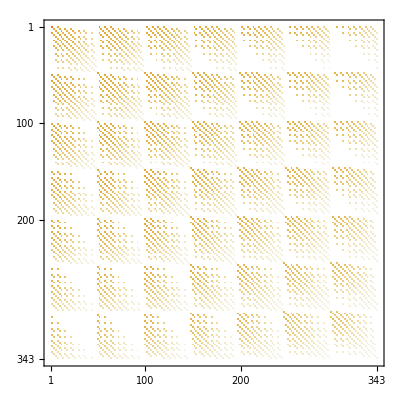

```mathematica
getρinit@@RandomReal[1,5]//Ptrace[#,{4}]&//MatrixPlot
```

```mathematica
covSIvac//MatrixForm
```

(1/2+Ns η κ+Nb (κ-η κ) | (Nb-Nb η+Ns η) √(-((-1+κ) κ)) | 0 | 0 | 0 | √Ns √(1+Ns) √η √κ (Cos[θ]-ⅈ Sin[θ])
(Nb-Nb η+Ns η) √(-((-1+κ) κ)) | 1/2+Nb (-1+η) (-1+κ)+Ns (η-η κ) | 0 | 0 | 0 | √Ns √(1+Ns) √η √(1-κ) (Cos[θ]-ⅈ Sin[θ])
0 | 0 | 1/2+Ns | √Ns √(1+Ns) √η √κ (Cos[θ]-ⅈ Sin[θ]) | √Ns √(1+Ns) √η √(1-κ) (Cos[θ]-ⅈ Sin[θ]) | 0
0 | 0 | √Ns √(1+Ns) √η √κ (Cos[θ]+ⅈ Sin[θ]) | 1/2+Ns η κ+Nb (κ-η κ) | (Nb-Nb η+Ns η) √(-((-1+κ) κ)) | 0
0 | 0 | √Ns √(1+Ns) √η √(1-κ) (Cos[θ]+ⅈ Sin[θ]) | (Nb-Nb η+Ns η) √(-((-1+κ) κ)) | 1/2+Nb (-1+η) (-1+κ)+Ns (η-η κ) | 0
√Ns √(1+Ns) √η √κ (Cos[θ]+ⅈ Sin[θ]) | √Ns √(1+Ns) √η √(1-κ) (Cos[θ]+ⅈ Sin[θ]) | 0 | 0 | 0 | 1/2+Ns)

```mathematica
Clear[μcov]
```

```mathematica
covSIvac/.Assign[{Ns,Nb,θ,η,κ},{.1,1,0,.1,.2}]//MatrixForm
```

(0.682 | 0.364 | 0 | 0 | 0 | 0.0469042
0.364 | 1.228 | 0 | 0 | 0 | 0.0938083
0 | 0 | 0.6 | 0.0469042 | 0.0938083 | 0
0 | 0 | 0.0469042 | 0.682 | 0.364 | 0
0 | 0 | 0.0938083 | 0.364 | 1.228 | 0
0.0469042 | 0.0938083 | 0 | 0 | 0 | 0.6)

Test that GaussianrhofockPy is working with 3-mode covariance matrix↓

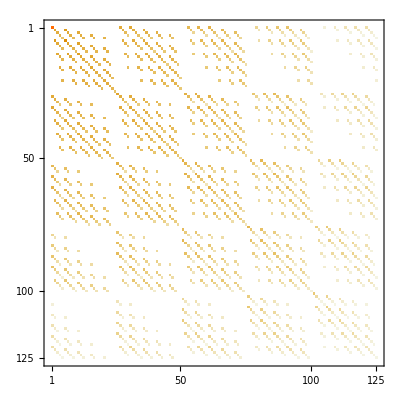

```mathematica
GaussianrhofockPy[covSIvac/.Assign[{Ns,Nb,θ,η,κ},{.1,1,0,.1,.2}],μSIvac,4]//MatrixPlot
```

↓Hamiltonians for evolving the SIvac state in time (Remember that the ordering of modes in the covariance matrix goes from fine  to coarse, which is the opposite of the order appearing in the Kronecker product to get the density matrix) Can’t use these if symbolic expression for the state to be evolved is unavailable.

```mathematica
dimvec=Table[cutoff+1,6];(*dimension of the density matrix is one more than max fock number since fock numbers range from 0 to nmax. dimvec={bdim,idlerdim,signaldim*)
{b1,b2,v1,ai,v2,as}=SparseArray[Table[If[j==i+1,√i,0],{i,#},{j,#}]]&/@dimvec;
{Idb1,Idb2,Idv1,Idi,Idv2,Ids}=SparseArray/@IdentityMatrix/@dimvec;
Hsfg1=#+#†&@(KroneckerProduct[#,#2†,Idv1,#3†]&@@{b1,ai,as});(*bai†as†+b†aias*)
Print["Hsfg: ",Hsfg1//MatrixPlot];
Hbeamsplit1=#-#†&[KroneckerProduct[Idb1,Idi,#†,#2]&@@{v1,as}];
Hbeamsplit2=#-#†&[KroneckerProduct[Idb1,Idi,#†,#2]&@@{v1,v2}];
Hsfg2=#+#†&[KroneckerProduct[#,Idb1,#2†,#3†]&@@{b2,ai,v1}];
```

Hsfg: -Graphics-

```mathematica
Clear[getρfinal,getFidel];
Ptrace[sparray_,modes_]:=SparseArray[PartialTraceComp[sparray//Normal,Table[cutoff+1,Log[cutoff+1,Length[sparray]]],modes]];
Options[getρfinal]={PrintTrace-> False};
getρfinal[Ns_,Nb_,θ_,η_,κ_,gt_,OptionsPattern[]]:=With[{
Usfg1=MatrixExp[-I N[gt] Hsfg1],
Ubs1=MatrixExp[-ArcCos[N[√(1-κ)]]Hbeamsplit1],
Ubs2=MatrixExp[-ArcCos[N[√κ]]Hbeamsplit2],
Usfg2=MatrixExp[-I N[gt] Hsfg2]},
With[{stage2=
Ptrace[Ubs1.Usfg1.getρinit[Ns,Nb,θ,η,κ].Usfg1†.Ubs1†,{1}]},
(*Print["printtraceoption: ",OptionValue[PrintTrace]];*)
stage2//Tr//Print["trace at stage 2 (after BS1): ",#]&//If[OptionValue[PrintTrace],#]&;
Ptrace[Usfg2.KroneckerProduct[vacuum,Ptrace[Ubs2.KroneckerProduct[stage2,vacuum].Ubs2†,{1}]].Usfg2†,{1,2}]]]
```

↓Function to get joint state of two enviroment modes

```mathematica
getEmodes[Ns_,Nb_,θ_,η_,κ_,gt_]:=With[{
Usfg1=MatrixExp[-I N[gt] Hsfg1],
Ubs1=MatrixExp[-ArcCos[N[√(1-κ)]] Hbeamsplit1],
Ubs2=MatrixExp[-ArcCos[N[√κ]](#-#†&@KroneckerProduct[Idi,v1†,v2,Ids])],
Usfg2=MatrixExp[-I N[gt] (#+#†&@KroneckerProduct[b2,Idi,v1†,v2†,Ids])],
Ubs3=MatrixExp[-ArcCos[N[√(1-κ)]](#-#†&[KroneckerProduct[v1†,v2,as]])]},
getρinit[Ns,Nb,θ,η,κ]//Usfg1.#.Usfg1†&//Ubs1.#.Ubs1†&//KroneckerProduct[Ptrace[#,{4}],vacuum]&//Ubs2.#.Ubs2†&//KroneckerProduct[vacuum,#]&//Usfg2.#.Usfg2†&//Ptrace[#,{4,5}]&//Ubs3.#.Ubs3†&//Ptrace[#,{2}]&]
```

```mathematica
Ptrace[SparseArray[KroneckerProduct[#,#2,#3,#4]&@@Table[RandomReal[1,{7,7}],4]],{1,2,3}]
```

SparseArray[…]

```mathematica
(*Symbollic expressions for the evolution unitaries, in case I want to implement compiled version of the evolution instead of using sparsearrays*)
Usfg1=Simplify[ExpToTrig[MatrixExp[-I gt Hsfg1]]];
Ubs1=Simplify[ExpToTrig[MatrixExp[-ArcCos[√(1-κ)]Hbeamsplit1]]];
Ubs2=Simplify[ExpToTrig[MatrixExp[-ArcCos[√κ]Hbeamsplit2]]];
Usfg2=Simplify[ExpToTrig[MatrixExp[-I gt Hsfg2]]];
```

```mathematica
MatrixExp[-I N[3π/7]  Hsfg1]
```

SparseArray[…]

```mathematica
getUsfg=Compile[{gt},Usfg1,CompilationOptions->{
"InlineExternalDefinitions" ->  True,
"ExpressionOptimization" ->  True}];
getUbs=Compile[{κ},Ubs2,CompilationOptions-> {
"InlineExternalDefinitions"-> True,
"ExpressionOptimization"-> True}]
```

```mathematica
getρfinalcomp=Compile[{Ns,Nb,θ,η,κ,gt},
With[{Usfg2=getUsfg[gt],Ubs1=getUbs[1-κ],Ubs2=getUbs[κ]},
With[{Usfg1=Usfg2},
With[{stage2=Ptrace[Ubs1.Usfg1.getρinit[Ns,Nb,θ,η,κ].Usfg1†.Ubs1†,{1}]},
Ptrace[
getUsfg[gt].KroneckerProduct[vacuum,Ptrace[Ubs2.KroneckerProduct[stage2,vacuum].Ubs2†,{1}]].Usfg2†,{1,2}]]]]]
```

↑Compiled evolution is not the way to go because symbolic unitaries take for ever to evaluate.

```mathematica
ClearSystemCache[]
```

```mathematica
final=getρfinal[0.1,5,π/3,.1,.1,π/2,PrintTrace-> False];
MatrixPlot[final,PlotLegends->Automatic]
```

trace at stage 2 (after BS1): 0.785964-4.48768×10^-20 ⅈ

-Graphics-

```mathematica
final//Tr
```

0.785964-4.48768×10^-20 ⅈ

```mathematica
twoemodes=getEmodes[0.1,2,π/3,.1,.1,π/2];
```

```mathematica
MatrixPlot[#,PlotLegends-> Automatic]&/@{Re[#],Im[#]}&@twoemodes
```

{-Graphics-,-Graphics-}

```mathematica
twoemodes//Tr
```

0.964931-4.41039×10^-19 ⅈ